# Project 2 - Distributions

## Report

Emil Lengman, emillen@kth.se
Simon Enerstrand, simonene@kth.se

## Section. Summary

For this project we were handed a module for randomizing numbers from six different distributions (randomNumber). We are going to use it to test different distribution models, divided in two sub-assignments.

### Section.Subsection Summary sub-assignment 1

#### Description

For this sub-assignment we are going to use the first (index zero in the module) distribution to test three models, and see which one fits the random data the best. The models are:

pdf(x)∝e^(-a x),x≥0

pdf(x)∝x e^(-a x),x≥0

pdf(x)∝x (x+b)e^(-a x),x≥0

When we’ve found the most fitting model we are going to compute the 95% confidence intervals for the constants in the chosen model.

#### Result

### Section.Subsection Summary sub-assignment 2

#### Description

For this sub-assignment we are going to generate data from all the different distributions and determine which distribution model fits the data the best for each data set (using the  straight line approach). Then we are going to determine the point estimates of the parameters, and compute 95% confidence intervals for those parameters.

#### Result

These are the resulting distribution models for the data (by index in the module):

Exponential distribution

Geometric distribution

Gamma distribution

Normal distribution

Binomial distribution

## Section. Distribution parameters

### Section.Subsection First model

#### Solution

#### Discussion

#### Code

```mathematica
ClearAll["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

### Section.Subsection Second model

#### Solution

#### Code

### Section.Subsection Third model

#### Solution

#### Code

### Section.Subsection Discussion

## Section. Which distribution?

### Section.Subsection Determine a distribution model

#### Solution

To determine the distribution model of the random data we can use the built-in function FindDistribution, which takes a list of values and returns a distribution. This only works reliably when we use a large enough sample size.

#### Code

##### Distribution 1

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
rand = randomNumber[1, n];
μ= Mean[rand];
FindDistribution[rand]
```

ExponentialDistribution[4.47466]

```mathematica
distribution = EstimatedDistribution[rand, ExponentialDistribution[λ]]
```

ExponentialDistribution[4.47466]

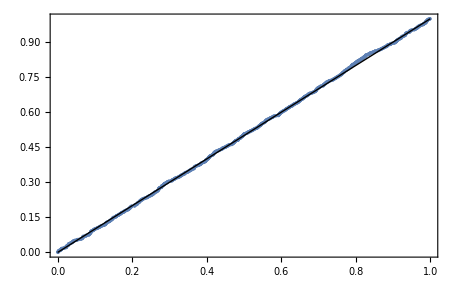

```mathematica
ProbabilityPlot[rand, distribution]
```

##### Distribution 2

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
rand = randomNumber[2, n];
FindDistribution[rand]
```

GeometricDistribution[0.0646747]

GeometricDistribution[0.0646747]

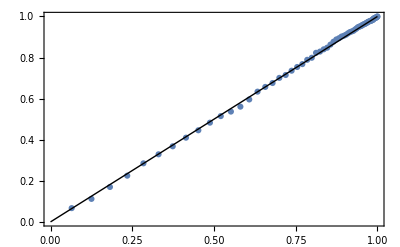

```mathematica
distribution=EstimatedDistribution[rand,GeometricDistribution[p]]
ProbabilityPlot[rand,distribution]
```

##### Distribution 3

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
numbers = randomNumber[3, n];
FindDistribution[numbers]
```

GammaDistribution[8.35735,1.56034]

```mathematica
distribution=EstimatedDistribution[numbers,GammaDistribution[α,β]]
```

GammaDistribution[7.98666,1.6063]

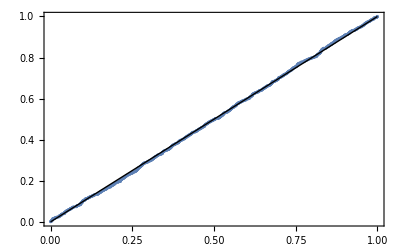

```mathematica
ProbabilityPlot[numbers, distribution]
```

##### Distribution 4

```mathematica
ClearAll["`*"]
```

```mathematica
n = 100;
```

```mathematica
numbers = randomNumber[4, n];
FindDistribution[numbers]
```

NormalDistribution[3.08368,4.75743]

```mathematica
distribution=EstimatedDistribution[numbers, NormalDistribution[μ,σ]]
```

NormalDistribution[3.07657,4.54242]

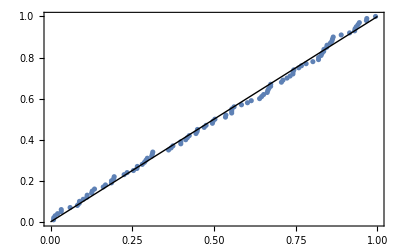

```mathematica
ProbabilityPlot[numbers, distribution]
```

##### Distribution 5

```mathematica
n = 1000;
```

```mathematica
numbers = randomNumber[5, n];
FindDistribution[numbers]
```

BinomialDistribution[14,0.236991]

```mathematica
distribution = EstimatedDistribution[numbers, BinomialDistribution[num, p]]
```

BinomialDistribution[12,0.272167]

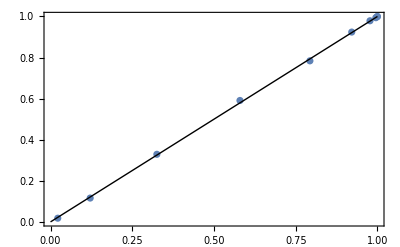

```mathematica
ProbabilityPlot[numbers, distribution]
```

##### Distribution 6

```mathematica
ClearAll["`*"]
```

```mathematica
n = 100;
```

```mathematica
numbers = randomNumber[6, n];
FindDistribution[numbers]
```

PoissonDistribution[9.06863]

```mathematica
distribution = EstimatedDistribution[numbers, PoissonDistribution[μ]]
```

PoissonDistribution[9.06]

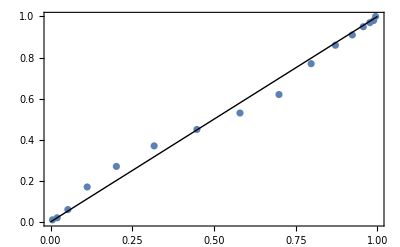

```mathematica
ProbabilityPlot[numbers, distribution]
```

### Section.Subsection Point estimates, and confidence intervals, for parameters

#### Solution

#### Code